```mathematica
<<Quaternions`
```

```mathematica
mandelbrot = Compile[{x,y,p, q,lim},
Module[{z, ct=0,ct2=1},
w=ConstantArray[0,400];
u=ConstantArray[0,400];
r=ConstantArray[0,400];
v=ConstantArray[0,400];
z=Quaternion[x,y,p,q];
w[[1]]= x;
u[[1]]= y;
r[[1]]= p;
v[[1]]= q;
While [Abs[z]<8.0&&ct<1,
z=z**z+Quaternion[x,y,p, q];
w[[2]]=Re[z];
u[[2]]=(List@@z)[[2]];
r[[2]]=(List@@z)[[3]];
v[[2]]=(List@@z)[[4]];
++ct];
While[Abs[z]<8.0&&1≤ct2≤lim,ct=ct2;
xn=(1-epsilon)w[[ct2+1]]+epsilon w[[ct2]];
yn=(1-epsilon)u[[ct2+1]]+epsilon u[[ct2]];
pn=(1-epsilon)r[[ct2+1]]+epsilon r[[ct2]];
qn=(1-epsilon)v[[ct2+1]]+epsilon v[[ct2]];
xn2=xn xn-yn yn-pn pn-qn qn+x;
yn2=2 xn yn+y;
pn2=2 xn pn+p;
qn2=2 xn qn+q;
z=Quaternion[xn2,yn2,pn2,qn2];
w[[ct2+2]]=xn2;
u[[ct2+2]]=yn2;
r[[ct2+2]]=pn2;
v[[ct2+2]]=qn2;
++ct2];
ct]];
Off[CompiledFunction::cfex]
```

```mathematica
vg={};
For[epsilon=0,epsilon<0.5,epsilon=epsilon+0.1,
gus=DensityPlot[mandelbrot[x,y,0.5,0.5,100],
{x,-2.,1.},{y,-1.5,1.5},{AspectRatio->1, ColorFunction-> (If[Mod[#1,2]==0&&Mod[#1,100]==0,Red,If[Mod[#1,2]==1,White,Blue]]&),ColorFunctionScaling->False,Frame->False,PlotPoints->10,PlotRange-> All}];
vg=Append[vg,gus]]
```

```mathematica
Length[vg]
```

5

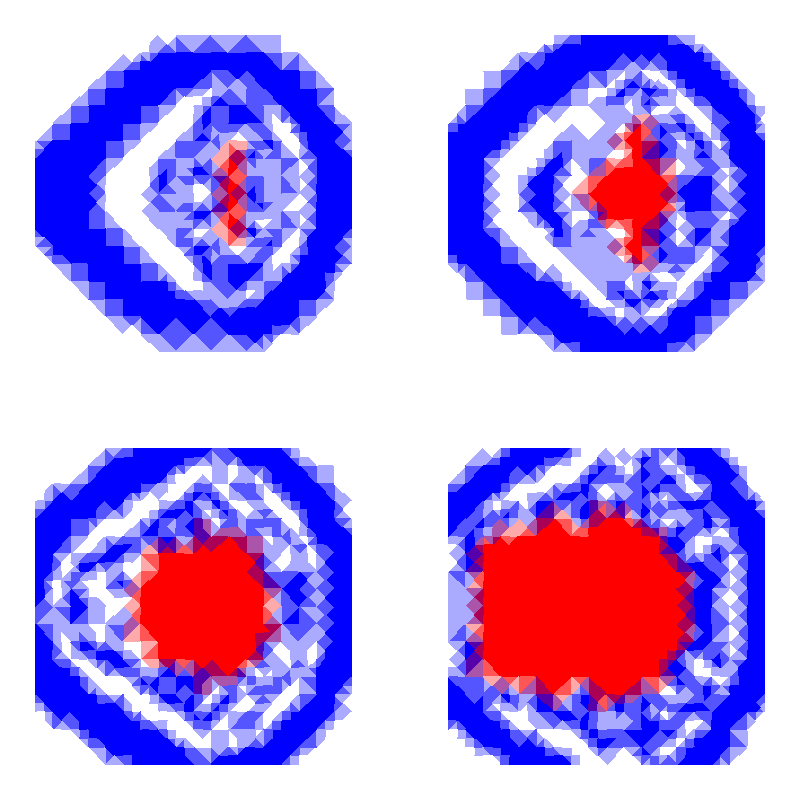

```mathematica
GraphicsGrid[{{vg[[1]],vg[[2]]},{vg[[3]],vg[[4]]}}]
```